```mathematica
(*通过实验测得的Red LED光谱数据*)
redSpdData=Import["D:\\smartLighting\\redSpdData.xls"]//Flatten[#,1]&;
redSpdData[[All,1]]=redSpdData[[All,1]]*10^-9;
maxRedSpd=Max[redSpdData[[All,2]]];    (*相对光谱峰值大小，应该为1*)

redCenterLamda=Nearest[redSpdData[[All,2]]->redSpdData[[All,1]],maxRedSpd];          (*峰值处对应的波长*)

redHwList=Nearest[redSpdData[[All,2]]->redSpdData[[All,1]],maxRedSpd/2,2];      (*spd数值为峰值波长的一半的左右两点波长坐标*)

redHwL=redCenterLamda-redHwList[[1]]//Abs;           (*波长半宽左边*)
redHwR=redHwList[[2]]-redCenterLamda  //Abs;           (*波长半宽右边*)
redHW=redHwList[[2]]-redHwList[[1]] //Abs;               (*半波宽*)

redSpdData[[All,2]]=redSpdData[[All,2]]/maxRedSpd;

gRed0=ListPlot[redSpdData,PlotRange->{{380*10^-9,780*10^-9},{0,1}},(*AxesOrigin->{370*10^-9,0},*)AxesLabel->{"λ","spd"},PlotStyle->{Orange},PlotLegends->"Expressions"];

(*红色LED的SPD数学模型*)
redSpdModel[x_,k1L_,k2L_,k1R_,k2R_]:=Piecewise[{{((Exp[-k1L*(x-redCenterLamda[[1]])^2/(redHwL*2)^2]+2*Exp[-k1L*(x-redCenterLamda[[1]])^2/(redHwL*2)^2]^5)/3)*Cosh[k2L*(x-redCenterLamda[[1]])^2/(redHwL*2)^2]^2.2,380*10^-9≤x<=redCenterLamda[[1]]},{((Exp[-k1R*(x-redCenterLamda[[1]])^2/(redHwR*2)^2]+2*Exp[-k1R*(x-redCenterLamda[[1]])^2/(redHwR*2)^2]^5)/3)*Cosh[k2R*(x-redCenterLamda[[1]])^2/(redHwR*2)^2]^2,redCenterLamda[[1]]<x<=780*10^-9}},0];


gRed1=Plot[redSpdModel[x,0.4233,-0.128,1.746,-0.2381],{x,380*10^-9,780*10^-9},PlotRange->{{380*10^-9,780*10^-9},{0,1}},PlotStyle->{ Green,Thickness[0.004]},PlotLegends->"Expressions"];

(*Show[gRed0,gRed1];*)
```

```mathematica
(*通过实验测得的Green LED光谱数据*)
(*greenSpdData=Import["D:\\smartLighting\\greenSpdData.xls"]//Flatten[#,1]&;
greenSpdData[[All,1]]=greenSpdData[[All,1]]*10^-9;
maxGreenSpd=Max[greenSpdData[[All,2]]];                          (*相对光谱峰值大小，应该为1*)

greenCenterLamda=Nearest[greenSpdData[[All,2]]->greenSpdData[[All,1]],maxGreenSpd];      
 greenCenterLamda= (greenCenterLamda[[1]]+greenCenterLamda[[2]])/2;(*峰值处对应的波长*)

greenHwList=Nearest[greenSpdData[[All,2]]->greenSpdData[[All,1]],maxGreenSpd/2,4]//Sort ;     (*spd数值为峰值波长的一半的左右的4个点波长坐标*)

greenHwL=greenCenterLamda-(greenHwList[[3]]+greenHwList[[4]])/2 //Abs ;         (*波长半宽左边*)
greenHwR=(greenHwList[[1]]+greenHwList[[2]])/2-greenCenterLamda //Abs ;         (*波长半宽右边*)
greenHW=(greenHwList[[3]]+greenHwList[[4]]-greenHwList[[1]]-greenHwList[[2]] )/2 ;            (*半波宽*)

greenSpdData[[All,2]]=greenSpdData[[All,2]]/maxGreenSpd;

gGreen0=ListPlot[greenSpdData,PlotRange->{{380*10^-9,780*10^-9},{0,1}},(*AxesOrigin->{370*10^-9,0},*)AxesLabel->{"λ","spd"},PlotStyle->{Orange},PlotLegends->"Expressions"];

(*绿色LED的SPD数学模型*)
greenSpdModel[x_,k1L_,k2L_,k1R_,k2R_]:=Piecewise[{{((Exp[-k1L*(x-greenCenterLamda)^2/(greenHwL*2)^2]+2*Exp[-k1L*(x-greenCenterLamda)^2/(greenHwL*2)^2]^5)/3)*Cosh[k2L*(x-greenCenterLamda)^2/(greenHwL*2)^2]^-0.1,380*10^-9≤x<=greenCenterLamda},{((Exp[-k1R*(x-greenCenterLamda)^2/(greenHwR*2)^2]+2*Exp[-k1R*(x-greenCenterLamda)^2/(greenHwR*2)^2]^5)/3)*Cosh[k2R*(x-greenCenterLamda)^2/(greenHwR*2)^2]^0.1,greenCenterLamda<x<=780*10^-9}},0];
gGreen1=Plot[greenSpdModel[x,0.9524,7.312,0.6667,-0.3175],{x,380*10^-9,780*10^-9},PlotRange->{{380*10^-9,780*10^-9},{0,1}},PlotStyle->{ Green,Thickness[0.004]},PlotLegends->"Expressions"];

Show[gGreen0,gGreen1];*)
```

```mathematica
(*通过实验测得的Blue LED光谱数据*)
blueSpdData=Import["D:\\smartLighting\\blueSpdData.xls"]//Flatten[#,1]&;
blueSpdData[[All,1]]=blueSpdData[[All,1]]*10^-9;
maxBlueSpd=Max[blueSpdData[[All,2]]];    (*相对光谱峰值大小，应该为1*)

blueCenterLamda=Nearest[blueSpdData[[All,2]]->blueSpdData[[All,1]],maxBlueSpd] ;   
(* blueCenterLamda= (blueCenterLamda[[1]]+blueCenterLamda[[2]])/2(*峰值处对应的波长*)*)

blueHwList=Nearest[blueSpdData[[All,2]]->blueSpdData[[All,1]],maxBlueSpd/2,4]//Sort ;     (*spd数值为峰值波长的一半的左右两点波长坐标*)

blueHwL=blueCenterLamda-(blueHwList[[3]]+blueHwList[[4]])/2 //Abs;        (*波长半宽左边*)
blueHwR=(blueHwList[[1]]+blueHwList[[2]])/2-blueCenterLamda //Abs ;      (*波长半宽右边*)
blueHW=(blueHwList[[3]]+blueHwList[[4]]-blueHwList[[1]]-blueHwList[[2]] )/2;             (*半波宽*)

blueSpdData[[All,2]]=blueSpdData[[All,2]]/maxBlueSpd;

gBlue0=ListPlot[blueSpdData,PlotRange->{{380*10^-9,780*10^-9},{0,1}},(*AxesOrigin->{370*10^-9,0},*)AxesLabel->{"λ","spd"},PlotStyle->{Orange},PlotLegends->"Expressions"];

(*蓝色LED的SPD*)
blueSpdModel[x_,k1L_,k2L_,k1R_,k2R_]:=Piecewise[{{((Exp[-k1L*(x-blueCenterLamda)^2/(blueHwL*3)^2]+2*Exp[-k1L*(x-blueCenterLamda)^2/(blueHwL*3)^2]^5)/3)*Cosh[k2L*(x-blueCenterLamda)^2/(blueHwL*3)^2]^-0.1,380*10^-9≤x<=blueCenterLamda[[1]]},{((Exp[-k1R*(x-blueCenterLamda)^2/(blueHwR*2)^2]+2*Exp[-k1R*(x-blueCenterLamda)^2/(blueHwR*2)^2]^5)/3)*Cosh[k2R*(x-blueCenterLamda)^2/(blueHwR*2)^2]^0.1,blueCenterLamda[[1]]<x<=780*10^-9}},0];
gBlue1=Plot[blueSpdModel[x,2.0899,5.566,0.7937,1.5873],{x,380*10^-9,780*10^-9},PlotRange->{{380*10^-9,780*10^-9},{0,1}},PlotStyle->{ Green,Thickness[0.004]},PlotLegends->"Expressions"];

Show[gBlue0,gBlue1];
```

```mathematica
(*通过实验测得的Amber LED光谱数据*)
(*amberSpdData=Import["D:\\smartLighting\\amberSpdData.xls"]//Flatten[#,1]&;
amberSpdData[[All,1]]=amberSpdData[[All,1]]*10^-9;
maxAmberSpd=Max[amberSpdData[[All,2]]];    (*相对光谱峰值大小，应该为1*)

amberCenterLamda=Nearest[amberSpdData[[All,2]]->amberSpdData[[All,1]],maxAmberSpd];         (*峰值处对应的波长*)



amberHwList=Nearest[amberSpdData[[All,2]]->amberSpdData[[All,1]],maxAmberSpd/2,2];      (*spd数值为峰值波长的一半的左右两点波长坐标*)

amberHwL=amberCenterLamda-amberHwList[[1]] ;        (*波长半宽左边*)
amberHwR=amberHwList[[2]]-amberCenterLamda ;        (*波长半宽右边*)
amberHW=amberHwList[[2]]-amberHwList[[1]];            (*半波宽*)

amberSpdData[[All,2]]=amberSpdData[[All,2]]/maxAmberSpd;

gAmber0=ListPlot[amberSpdData,PlotRange->{{380*10^-9,780*10^-9},{0,1}},(*AxesOrigin->{370*10^-9,0},*)AxesLabel->{"λ","spd"},PlotStyle->{Orange},PlotLegends->"Expressions"];


(*琥珀色LED的SPD数学模型*)
amberSpdModel[x_,k1L_,k2L_,k1R_,k2R_]:=Piecewise[{{((Exp[-k1L*(x-amberCenterLamda)^2/(amberHwL*2)^2]+2*Exp[-k1L*(x-amberCenterLamda)^2/(amberHwL*2)^2]^9*0)/1)*Cosh[k2L*(x-amberCenterLamda)^2/(amberHwL*2)^2]^1.2,380*10^-9≤x<=amberCenterLamda[[1]]},{((Exp[-k1R*(x-amberCenterLamda)^2/(amberHwR*2)^2]+2*Exp[-k1R*(x-amberCenterLamda)^2/(amberHwR*2)^2]^5)/3)*Cosh[k2R*(x-amberCenterLamda)^2/(amberHwR*2)^2]^0.4,amberCenterLamda[[1]]<x<=780*10^-9}},0];

(*amberSpdModel[6.078*^-7,4.0741,-2.698,1.4815,1.92]*)

gAmber1=Plot[amberSpdModel[x,4.0741,-2.698,0.7937,-0.106],{x,380*10^-9,780*10^-9},PlotRange->{{380*10^-9,780*10^-9},{0,1}},PlotStyle->{ Green,Thickness[0.004]},PlotLegends->"Expressions"];

Show[gAmber0,gAmber1];*)
```

```mathematica
(*Lime LED*)

limeCenterLamda={545*10^-9};
limeHwL=30*10^-9;
limeHwR=60*10^-9;

limeSpdModel[x_,k1L_,k2L_,k1R_,k2R_]:=Piecewise[{{((Exp[-k1L*(x-limeCenterLamda)^2/(limeHwL*2)^2]+2*Exp[-k1L*(x-limeCenterLamda)^2/(limeHwL*2)^2]^5)/3)*Cosh[k2L*(x-limeCenterLamda)^2/(limeHwL*2)^2]^-2,380*10^-9≤x<=limeCenterLamda[[1]]},{((Exp[-k1R*(x-limeCenterLamda)^2/(limeHwR*2)^2]+2*Exp[-k1R*(x-limeCenterLamda)^2/(limeHwR*2)^2]^5)/3)*Cosh[k2R*(x-limeCenterLamda)^2/(limeHwR*2)^2]^0.4,limeCenterLamda[[1]]<x<=780*10^-9}},0];
```

```mathematica
(*pcAmber LED的SPD数学模型*)
pcAmberCenterLamda={595*10^-9};
pcAmberHwL=30*10^-9;
pcAmberHwR=50*10^-9;

pcAmberSpdModel[x_,k1L_,k2L_,k1R_,k2R_]:=Piecewise[{{((Exp[-k1L*(x-pcAmberCenterLamda)^2/(pcAmberHwL*2)^2]+2*Exp[-k1L*(x-pcAmberCenterLamda)^2/(pcAmberHwL*2)^2]^5)/3)*Cosh[k2L*(x-pcAmberCenterLamda)^2/(pcAmberHwL*2)^2]^-2,380*10^-9≤x<=pcAmberCenterLamda[[1]]},{((Exp[-k1R*(x-pcAmberCenterLamda)^2/(pcAmberHwR*2)^2]+2*Exp[-k1R*(x-pcAmberCenterLamda)^2/(pcAmberHwR*2)^2]^5)/3)*Cosh[k2R*(x-pcAmberCenterLamda)^2/(pcAmberHwR*2)^2]^-0.4,pcAmberCenterLamda[[1]]<x<=780*10^-9}},0];
```

```mathematica
(*cyan LED的SPD数学模型*)
cyanCenterLamda={505*10^-9};
cyanHwL=12*10^-9;
cyanHwR=18*10^-9;

cyanSpdModel[x_,k1L_,k2L_,k1R_,k2R_]:=Piecewise[{{((Exp[-k1L*(x-cyanCenterLamda)^2/(cyanHwL*2)^2]+2*Exp[-k1L*(x-cyanCenterLamda)^2/(cyanHwL*2)^2]^5)/3)*Cosh[k2L*(x-cyanCenterLamda)^2/(cyanHwL*2)^2]^0,380*10^-9≤x<=cyanCenterLamda[[1]]},{((Exp[-k1R*(x-cyanCenterLamda)^2/(cyanHwR*2)^2]+2*Exp[-k1R*(x-cyanCenterLamda)^2/(cyanHwR*2)^2]^5)/3)*Cosh[k2R*(x-cyanCenterLamda)^2/(cyanHwR*2)^2]^0,cyanCenterLamda[[1]]<x<=780*10^-9}},0];
```

```mathematica
multiLedSpdModel[x_,kRed_,kBlue_,kLime_,kPcAmber_,kCyan_]:=kRed*redSpdModel[x,0.4233,-0.128,1.746,-0.2381]+kBlue*blueSpdModel[x,2.0899,5.566,0.7937,1.5873]+kLime*limeSpdModel[x,2.17,-1.75,1.4815,1.92]+kPcAmber*pcAmberSpdModel[x,2.17,-1.53,1.11,1.53]+kCyan*cyanSpdModel[x,0.79,-1.53,1.11,1.53];

Manipulate[
Plot[multiLedSpdModel[x,kRed,kBlue,kLime,kPcAmber,kCyan],{x,380*10^-9,780*10^-9},PlotRange->{{380*10^-9,780*10^-9},{0,2}},PlotStyle->{ Green,Thickness[0.004]}(*,PlotLegends->"Expressions"*)],{{kRed,0.6,"kRed"},0,1,0.1},{{kBlue,0.2,"kBlue"},0,1,0.1},{{kLime,0.6,"kLime"},0,1,0.1},{{kPcAmber,0.6,"kPcAmber"},0,1,0.1},{{kCyan,0.3,"kCyan"},0,1,0.1},(*FrameLabel->"multiLedSpdModel(x,kRed,kGreen,kBlue,kAmber)",*) ControlPlacement->Right]
```

```mathematica
cie1931Table=Import["D:\\smartLighting\\cie1931_obersever.xls"]//Flatten[#,1]&(*//MatrixForm*)//Compress;
cie1931Data=Uncompress[cie1931Table];
cie1931Length=cie1931Data[[All,1]]*10^-9;
(*deltaWaveLength=*)
cie1931xBar=cie1931Data[[All,2]];
cie1931yBar=cie1931Data[[All,3]];
cie1931zBar=cie1931Data[[All,4]];

cie1964uBar=(2/3)*cie1931xBar;
cie1964vBar=cie1931yBar;
cie1964wBar=-0.5*cie1931xBar+(3/2)*cie1931yBar+0.5*cie1931zBar;

(*% 2002 CODATA recommended values*)
h=6.6260693*10^-34;
c=299792458;
k=1.3806505*10^-23;
c1=2*Pi*h*c^2;
c2=h*c/k;

(*xxxxxxxxxxxxxx*)
MrecpK=Range[600]//Prepend[#,0.01]& ;(*[0.01 1:600];            % mega reciprical Kelvin values of isotemperature lines*)
T=1./(MrecpK*10^-6);

dwave=1;
u=v=sl=m=Table[0,{i,Length[T]}];

For[i=1,i≤(*2*)Length[T],i++,
spdref=c1*cie1931Length^-5/(Exp[c2/(T[[i]]*cie1931Length)]-1);
spdref=spdref/Max[spdref];

(*% Equations from Wyszecki and Sitles,Color Science,2nd ed.1982,page % 226 and 227*)
U=spdref*cie1964uBar//Total;
V=spdref*cie1964vBar//Total;
W=spdref*cie1964wBar//Total;
R=U+V+W;
u[[i]]=U/R;
v[[i]]=V/R;

Uprime=c1*c2*T[[i]]^-2*Total[cie1931Length^-6*cie1964uBar*Exp[c2/(cie1931Length*T[[i]])]*(Exp[c2/(cie1931Length*T[[i]])]-1)^-2]*dwave;      (*% dU/dT*)
Vprime=Total[c1*c2*T[[i]]^-2*cie1931Length^-6*cie1964vBar*Exp[c2/(cie1931Length*T[[i]])]*(Exp[c2/(cie1931Length*T[[i]])]-1)^-2]*dwave;           (*% dV/dT*)
Wprime=Total[c1*c2*T[[i]]^-2*cie1931Length^-6*cie1964wBar*Exp[c2/(cie1931Length*T[[i]])]*(Exp[c2/(cie1931Length*T[[i]])]-1)^-2]*dwave;           (*% dW/dT*)
Rprime=Uprime+Vprime+Wprime;
sl[[i]]=(Vprime*R-V*Rprime)/(Uprime*R-U*Rprime);                               (*%普朗克轨迹线上垂足处的切线斜率*)
m[[i]]=-1/sl[[i]];                                                                                                                          (* %等温线斜率*)
]

ut=u;
vt=v;
tt=m;
isoTempLinesTable=Transpose@@{{T,u,v,m}};
```

```mathematica
(*% Calculate Chromaticity Coordinates*)
xBarData={cie1931Data[[All,1]],cie1931Data[[All,2]]}//Transpose;
yBarData={cie1931Data[[All,1]],cie1931Data[[All,3]]}//Transpose;
zBarData={cie1931Data[[All,1]],cie1931Data[[All,4]]}//Transpose;

xBarInterFunc=Interpolation[xBarData];
xBarInterFunc[Range[380,780,10]];
yBarInterFunc=Interpolation[yBarData];
zBarInterFunc=Interpolation[zBarData];

Attributes[multiLedSpdModel]={Listable};
(*multiLedSpdModel[Range[380,780,10]*10^-9,0.6,0.2,0.6,0.6,0.3]*)
lampX=multiLedSpdModel[Range[380,780,10]*10^-9,0.6,0.6,0.6,0.6,0.6]*xBarInterFunc[Range[380,780,10]]*10//Total;
lampY=multiLedSpdModel[Range[380,780,10]*10^-9,0.6,0.6,0.6,0.6,0.6]*yBarInterFunc[Range[380,780,10]]*10//Total;
lampZ=multiLedSpdModel[Range[380,780,10]*10^-9,0.6,0.6,0.6,0.6,0.6]*zBarInterFunc[Range[380,780,10]]*10//Total;

xLamp=lampX/(lampX+lampY+lampZ)
yLamp=lampY/(lampX+lampY+lampZ)
zLamp=lampZ/(lampX+lampY+lampZ);
uLamp=4*xLamp/(-2*xLamp+12*yLamp+3)
vLamp=6*yLamp/(-2*xLamp+12*yLamp+3)
```

{0.416296}

{0.427787}

{0.228081}

{0.351565}

```mathematica
(*% Find adjacent lines to (us,vs)*)
n=Length [T];
index=0;
d1=((vLamp-vt[[1]])-tt[[1]]*(uLamp-ut[[1]]))/Sqrt[1+tt[[1]]*tt[[1]]];
(*d1[[1]]*)
For[i=2,i≤n,i++,
d2=((vLamp-vt[[i]])-tt[[i]]*(uLamp-ut[[i]]))/Sqrt[1+tt[[i]]*tt[[i]]];
If[d1[[1]]/d2[[1]]<0,{index=i,Break[]},index=111,index=-1(*d1=d2*)]
]

Tc=1/(1/T[[index-1]]+d1/(d1-d2)*(1/T[[index]]-1/T[[index-1]]))
```

{3546.13}

```mathematica
(*% Third,calculate the Color Rendering Indices (CRI and its 14 indices),Calculate Reference Source Spectrum,spdref.*)

c1=3.7418*10^-16;
c2=1.4388*10^-2;

Tc={2856.3};
spdLength=Range[380,780,10];
spdref=c1*(10^-9*spdLength)^-5/(Exp[c2/(Tc[[1]]*(10^-9*spdLength))]-1);
```

```mathematica
TCS={{360,116,53,58,57,143,79,150,75,69,42,74,189,71,36},{365,136,55,59,59,187,81,177,78,72,43,79,175,76,36},{370,159,59,61,62,233,89,218,84,73,45,86,158,82,36},{375,190,64,63,67,269,113,293,90,70,47,98,139,90,36},{380,219,70,65,74,295,151,378,104,66,50,111,120,104,36},{385,239,79,68,83,306,203,459,129,62,54,121,103,127,36},{390,252,89,70,93,310,265,524,170,58,59,127,90,161,37},{395,256,101,72,105,312,339,546,240,55,63,129,82,211,38},{400,256,111,73,116,313,410,551,319,52,66,127,76,264,39},{405,254,116,73,121,315,464,555,416,52,67,121,68,313,39},{410,252,118,74,124,319,492,559,462,51,68,116,64,341,40},{415,248,120,74,126,322,508,560,482,50,69,112,65,352,41},{420,244,121,74,128,326,517,561,490,50,69,108,75,359,42},{425,240,122,73,131,330,524,558,488,49,70,105,93,361,42},{430,237,122,73,135,334,531,556,482,48,72,104,123,364,43},{435,232,122,73,139,339,538,551,473,47,73,104,160,365,44},{440,230,123,73,144,346,544,544,462,46,76,105,207,367,44},{445,226,124,73,151,352,551,535,450,44,78,106,256,369,45},{450,225,127,74,161,360,556,522,439,42,83,110,300,372,45},{455,222,128,75,172,369,556,506,426,41,88,115,331,374,46},{460,220,131,77,186,381,554,488,413,38,95,123,346,376,47},{465,218,134,80,205,394,549,469,397,35,103,134,347,379,48},{470,216,138,85,229,403,541,448,382,33,113,148,341,384,50},{475,214,143,94,254,410,531,429,366,31,125,167,328,389,52},{480,214,150,109,281,415,519,408,352,30,142,192,307,397,55},{485,214,159,126,308,418,504,385,337,29,162,219,282,405,57},{490,216,174,148,332,419,488,363,325,28,189,252,257,416,62},{495,218,190,172,352,417,469,341,310,28,219,291,230,429,67},{500,223,207,198,370,413,450,324,299,28,262,325,204,443,75},{505,225,225,221,383,409,431,311,289,29,305,347,178,454,83},{510,226,242,241,390,403,414,301,283,30,365,356,154,461,92},{515,226,253,260,394,396,395,291,276,30,416,353,129,466,100},{520,225,260,278,395,389,377,283,270,31,465,346,109,469,108},{525,225,264,302,392,381,358,273,262,31,509,333,90,471,121},{530,227,267,339,385,372,341,265,256,32,546,314,75,474,133},{535,230,269,370,377,363,325,260,251,32,581,294,62,476,142},{540,236,272,392,367,353,309,257,250,33,610,271,51,483,150},{545,245,276,399,354,342,293,257,251,34,634,248,41,490,154},{550,253,282,400,341,331,279,259,254,35,653,227,35,506,155},{555,262,289,393,327,320,265,260,258,37,666,206,29,526,152},{560,272,299,380,312,308,253,260,264,41,678,188,25,553,147},{565,283,309,365,296,296,241,258,269,44,687,170,22,582,140},{570,298,322,349,280,284,234,256,272,48,693,153,19,618,133},{575,318,329,332,263,271,227,254,274,52,698,138,17,651,125},{580,341,335,315,247,260,225,254,278,60,701,125,17,680,118},{585,367,339,299,229,247,222,259,284,76,704,114,17,701,112},{590,390,341,285,214,232,221,270,295,102,705,106,16,717,106},{595,409,341,272,198,220,220,284,316,136,705,100,16,729,101},{600,424,342,264,185,210,220,302,348,190,706,96,16,736,98},{605,435,342,257,175,200,220,324,384,256,707,92,16,742,95},{610,442,342,252,169,194,220,344,434,336,707,90,16,745,93},{615,448,341,247,164,189,220,362,482,418,707,87,16,747,90},{620,450,341,241,160,185,223,377,528,505,708,85,16,748,89},{625,451,339,235,156,183,227,389,568,581,708,82,16,748,87},{630,451,339,229,154,180,233,400,604,641,710,80,18,748,86},{635,451,338,224,152,177,239,410,629,682,711,79,18,748,85},{640,451,338,220,151,176,244,420,648,717,712,78,18,748,84},{645,451,337,217,149,175,251,429,663,740,714,78,18,748,84},{650,450,336,216,148,175,258,438,676,758,716,78,19,748,84},{655,450,335,216,148,175,263,445,685,770,718,78,20,748,84},{660,451,334,219,148,175,268,452,693,781,720,81,23,747,85},{665,451,332,224,149,177,273,457,700,790,722,83,24,747,87},{670,453,332,230,151,180,278,462,705,797,725,88,26,747,92},{675,454,331,238,154,183,281,466,709,803,729,93,30,747,96},{680,455,331,251,158,186,283,468,712,809,731,102,35,747,102},{685,457,330,269,162,189,286,470,715,814,735,112,43,747,110},{690,458,329,288,165,192,291,473,717,819,739,125,56,747,123},{695,460,328,312,168,195,296,477,719,824,742,141,74,746,137},{700,462,328,340,170,199,302,483,721,828,746,161,97,746,152},{705,463,327,366,171,200,313,489,720,830,748,182,128,746,169},{710,464,326,390,170,199,325,496,719,831,749,203,166,745,188},{715,465,325,412,168,198,338,503,722,833,751,223,210,744,207},{720,466,324,431,166,196,351,511,725,835,753,242,257,743,226},{725,466,324,447,164,195,364,518,727,836,754,257,305,744,243},{730,466,324,460,164,195,376,525,729,836,755,270,354,745,260},{735,466,323,472,165,196,389,532,730,837,755,282,401,748,277},{740,467,322,481,168,197,401,539,730,838,755,292,446,750,294},{745,467,321,488,172,200,413,546,730,839,755,302,485,750,310},{750,467,320,493,177,203,425,553,730,839,756,310,520,749,325},{755,467,318,497,181,205,436,559,730,839,757,314,551,748,339},{760,467,316,500,185,208,447,565,730,839,758,317,577,748,353},{765,467,315,502,189,212,458,570,730,839,759,323,599,747,366},{770,467,315,505,192,215,469,575,730,839,759,330,618,747,379},{775,467,314,510,194,217,477,578,730,839,759,334,633,747,390},{780,467,314,516,197,219,485,581,730,839,759,338,645,747,399},{785,467,313,520,200,222,493,583,730,839,759,343,656,746,408},{790,467,313,524,204,226,500,585,731,839,759,348,666,746,416},{795,466,312,527,210,231,506,587,731,839,759,353,674,746,422},{800,466,312,531,218,237,512,588,731,839,759,359,680,746,428},{805,466,311,535,225,243,517,589,731,839,759,365,686,745,434},{810,466,311,539,233,249,521,590,731,838,758,372,691,745,439},{815,466,311,544,243,257,525,590,731,837,757,380,694,745,444},{820,465,311,548,254,265,529,590,731,837,757,388,697,745,448},{825,464,311,552,264,273,532,591,731,836,756,396,700,745,451},{830,464,310,555,274,280,535,592,731,836,756,403,702,745,454}};


TCS1=Table[0,{i,Length[Range[380,780,10]]},{j,14}];
For[i=1,i<15,i++,
TCS1[[All,i]]=Interpolation[Transpose[{TCS[[All,1]],TCS[[All,i+1]]}]]/@Range[380,780,10]//N[#]&;
]

(*TCS1;*)
```

```mathematica
(*Calculate u,v chromaticity coordinates of samples under test illuminant,uk,vk and  reference illuminant,ur,vr.*)
uki=Table[0,{i,Length[Range[380,780,10]]}];
vki=Table[0,{i,Length[Range[380,780,10]]}];
Yki=Table[0,{i,14}];
uri=Table[0,{i,Length[Range[380,780,10]]}];
vri=Table[0,{i,Length[Range[380,780,10]]}];
Yri=Table[0,{i,14}];
ukip=Table[0,{i,14}];
vkip=Table[0,{i,14}];
Wstarr=Table[0,{i,14}];
Ustarr=Table[0,{i,14}];
Vstarr=Table[0,{i,14}];
Wstark=Table[0,{i,14}];
Ustark=Table[0,{i,14}];
Vstark=Table[0,{i,14}];
```

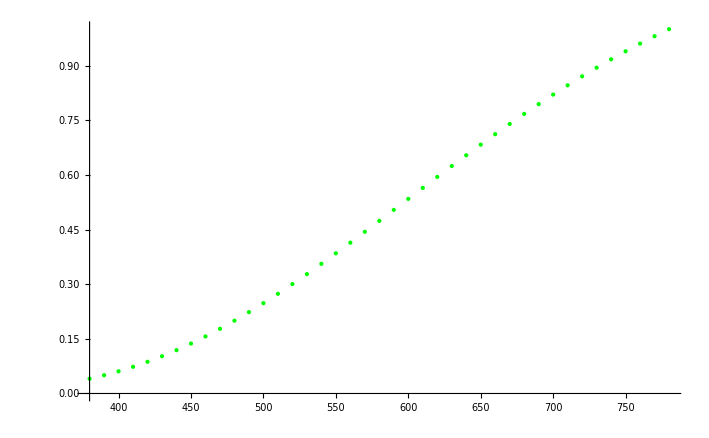

{0.0405789,0.0500639,0.060925,0.073212,0.0869579,0.102178,0.118871,0.137017,0.156583,0.177518,0.199759,0.223232,0.247851,0.273522,0.300144,0.32761,0.355811,0.384633,0.413964,0.44369,0.473699,0.503883,0.534134,0.564351,0.594436,0.624297,0.653847,0.683004,0.711693,0.739844,0.767395,0.794287,0.820469,0.845895,0.870525,0.894325,0.917265,0.93932,0.960471,0.980701,1.}

{{380,1.9638×10^-8},{390,4.96282×10^-7},{400,8.61193×10^-6},{410,0.000102641},{420,0.000840705},{430,0.00473873},{440,0.0185573},{450,0.0569106},{460,0.175722},{470,0.327005},{480,0.271102},{490,0.260933},{500,0.461106},{510,0.509364},{520,0.425869},{530,0.485259},{540,0.630963},{550,0.651918},{560,0.645074},{570,0.668884},{580,0.771822},{590,0.887832},{600,0.859472},{610,0.797296},{620,0.783053},{630,1.},{640,0.794817},{650,0.380589},{660,0.247262},{670,0.181492},{680,0.140633},{690,0.109966},{700,0.0856909},{710,0.0663587},{720,0.0511045},{730,0.0392284},{740,0.0300878},{750,0.0231003},{760,0.0177674},{770,0.0136867},{780,0.010548}}

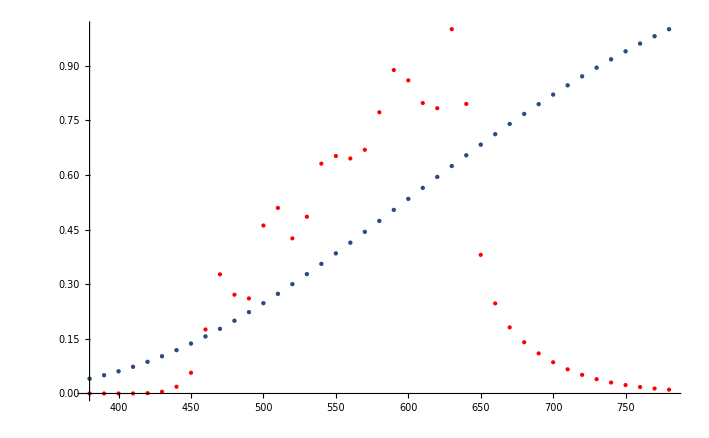

```mathematica
testAspd={{380,0.00132948037347175},{390,0.00164023432576807},{400,0.00199607408541092},{410,0.00239863299576014},{420,0.00284898784428011},{430,0.00334764547822949},{440,0.00389454498476917},{450,0.0044890736644276},{460,0.00513009474369056},{470,0.00581598464137424},{480,0.00654467759688934},{490,0.00731371555834619},{500,0.00812030138807687},{510,0.00896135364886274},{520,0.00983356146587939},{530,0.0107334382008557},{540,0.0116573729136429},{550,0.0126016788131223},{560,0.0135626381078808},{570,0.0145365428535139},{580,0.0155197315558729},{590,0.0165086214276558},{600,0.0174997363101301},{610,0.0184897303639286},{620,0.0194754077047119},{630,0.0204537382132532},{640,0.0214218697874947},{650,0.022377137328638},{660,0.0233170687665763},{670,0.0242393884339735},{680,0.0251420180949075},{690,0.0260230759248419},{700,0.026880873725211},{710,0.0277139126393038},{720,0.0285208776174515},{730,0.0293006308595934},{740,0.0300522044428256},{750,0.0307747923210527},{760,0.0314677418638086},{770,0.0321305450820022},{780,0.0327628296700076}};

(*{Range[380,780,10],spdref/Max[spdref]}//Transpose*)
gRefSpd=ListPlot[{Range[380,780,10],spdref/Max[spdref]}//Transpose,PlotStyle->{Green,Thick},PlotLegends->"Expressions"]

testAspd[[All,2]]=testAspd[[All,2]]/Max[testAspd[[All,2]]]
ga=ListPlot[testAspd];

gmData={Range[380,780,10],multiLedSpdModel[Range[380,780,10]*10^-9,0.4,0.2,0.4,0.4,0.3]/Max[multiLedSpdModel[Range[380,780,10]*10^-9,0.4,0.2,0.4,0.4,0.3]]//Flatten}//Transpose
gm=ListPlot[gmData,PlotStyle->{Red,Dashed,Thick}(*,PlotRange->{380,780}*)];

Show[gRefSpd,ga,gm]
```

```mathematica
(*X=multiLedSpdModel[cie1931Length,0.6,0.2,0.6,0.6,0.3]*cie1931xBar//Total;
Y=multiLedSpdModel[cie1931Length,0.6,0.2,0.6,0.6,0.3]*cie1931yBar//Total;
Z=multiLedSpdModel[cie1931Length,0.6,0.2,0.6,0.6,0.3]*cie1931zBar//Total;*)

xBarData={cie1931Data[[All,1]],cie1931Data[[All,2]]}//Transpose;
yBarData={cie1931Data[[All,1]],cie1931Data[[All,3]]}//Transpose;
zBarData={cie1931Data[[All,1]],cie1931Data[[All,4]]}//Transpose;

xBarInterFunc=Interpolation[xBarData];
xBarInterFunc[Range[380,780,10]];
yBarInterFunc=Interpolation[yBarData];
zBarInterFunc=Interpolation[zBarData];

X=multiLedSpdModel[Range[380,780,10]*10^-9,0.6,0.6,0.6,0.6,0.6]*xBarInterFunc[Range[380,780,10]]*10(*横轴单位：nm*)//Total;
Y=multiLedSpdModel[Range[380,780,10]*10^-9,0.6,0.6,0.6,0.6,0.6]*yBarInterFunc[Range[380,780,10]]*10(*横轴单位：nm*)//Total;
Z=multiLedSpdModel[Range[380,780,10]*10^-9,0.6,0.6,0.6,0.6,0.6]*zBarInterFunc[Range[380,780,10]]*10(*横轴单位：nm*)//Total;
x=X/(X+Y+Z)
y=Y/(X+Y+Z)

Yknormal=100/Y;
Yk=Y*Yknormal
uk=4*X/(X+15*Y+3*Z)
vk=6*Y/(X+15*Y+3*Z)
```

{0.416296}

{0.427787}

{100.}

{0.228081}

{0.351565}

```mathematica
X=spdref*xBarInterFunc[Range[380,780,10]]*10//Total;
Y=spdref*yBarInterFunc[Range[380,780,10]]*10//Total;
Z=spdref*zBarInterFunc[Range[380,780,10]]*10//Total;
Yrnormal=100/Y;
Yr=Y*Yrnormal
ur=4*X/(X+15*Y+3*Z)
vr=6*Y/(X+15*Y+3*Z)
```

100.

0.255917

0.349545

```mathematica
For[i=1,i<15,i++,
X=multiLedSpdModel[Range[380,780,10]*10^-9,0.6,0.6,0.6,0.6,0.6]*xBarInterFunc[Range[380,780,10]]*10*TCS1[[All,i]]//Total;
Y=multiLedSpdModel[Range[380,780,10]*10^-9,0.6,0.6,0.6,0.6,0.6]*yBarInterFunc[Range[380,780,10]]*10*TCS1[[All,i]]//Total;
Z=multiLedSpdModel[Range[380,780,10]*10^-9,0.6,0.6,0.6,0.6,0.6]*zBarInterFunc[Range[380,780,10]]*10*TCS1[[All,i]]//Total;
Yki[[i]]=Y*Yknormal;
uki[[i]]=4*X/(X+15*Y+3*Z);
  vki[[i]]=6*Y/(X+15*Y+3*Z);

X=spdref*xBarInterFunc[Range[380,780,10]]*10*TCS1[[All,i]]//Total;
Y=spdref*yBarInterFunc[Range[380,780,10]]*10*TCS1[[All,i]]//Total;
Z=spdref*zBarInterFunc[Range[380,780,10]]*10*TCS1[[All,i]]//Total;
Yri[[i]]=Y*Yrnormal;
   uri[[i]]=4*X/(X+15*Y+3*Z);
   vri[[i]]=6*Y/(X+15*Y+3*Z);
]

Yki
Yri
uki
vki
uri
vri
```

{{31630.4},{30036.4},{30544.3},{27994.9},{29180.5},{28001.2},{29242.5},{32197.1},{13416.},{62028.7},{18613.1},{5151.61},{59918.2},{11668.}}

{32703.7,30563.7,30494.1,27002.4,28149.,27228.5,29803.3,33898.3,16624.8,63711.8,17599.2,4461.35,61330.9,11647.4}

{{0.274338},{0.250602},{0.215888},{0.179424},{0.185083},{0.194209},{0.242377},{0.271655},{0.432397},{0.256657},{0.152414},{0.120797},{0.260843},{0.212856},0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

{{0.354643},{0.361542},{0.368573},{0.358914},{0.347189},{0.335199},{0.339138},{0.343756},{0.350279},{0.367865},{0.35974},{0.272841},{0.356748},{0.365859},0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

{0.304021,0.277253,0.237714,0.201328,0.209235,0.225102,0.277396,0.310635,0.46734,0.281753,0.174482,0.147226,0.289085,0.235306,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

{0.352406,0.360155,0.367461,0.359574,0.34612,0.332089,0.334807,0.3402,0.34757,0.366505,0.359821,0.273254,0.355168,0.364689,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
(*% Check tolorence for reference illuminant*)
DC=Sqrt[(uk-ur)^2+(vk-vr)^2];

(*% Apply adaptive (perceived) color shift.*)
ck=(4-uk-10*vk)/vk;
dk=(1.708*vk+0.404-1.481*uk)/vk;
cr=(4-ur-10*vr)/vr;
dr=(1.708*vr+0.404-1.481*ur)/vr;

For[i=1,i<15,i++,
cki=(4-uki[[i]]-10*vki[[i]])/vki[[i]];
   dki=(1.708*vki[[i]]+0.404-1.481*uki[[i]])/vki[[i]];
   ukip[[i]]=(10.872+0.404*cr/ck*cki-4*dr/dk*dki)/(16.518+1.481*cr/ck*cki-dr/dk*dki);
   vkip[[i]]=5.520/(16.518+1.481*cr/ck*cki-dr/dk*dki);
]

(*% Transformation into 1964 Uniform space coordinates.*)

For[i=1,i<15,i++,
Wstarr[[i]]=25*Yri[[i]]^0.333333-17;
   Ustarr[[i]]=13*Wstarr[[i]]*(uri[[i]]-ur);
   Vstarr[[i]]=13*Wstarr[[i]]*(vri[[i]]-vr);

   Wstark[[i]]=25*Yki[[i]]^0.333333-17;
   Ustark[[i]]=13*Wstark[[i]]*(ukip[[i]]-ur);(*% after applying the adaptive color shift,u'k=ur*)
   Vstark[[i]]=13*Wstark[[i]]*(vkip[[i]]-vr);(*% after applying the adaptive color shift,v'k=vr*)

]

(*% Determination of resultant color shift,delta E.*)

deltaE=Table[0,{i,14}];
R=Table[0,{i,14}];
For[i=1,i<15,i++,
deltaE[[i]]=Sqrt[(Ustarr[[i]]-Ustark[[i]])^2+(Vstarr[[i]]-Vstark[[i]])^2+(Wstarr[[i]]-Wstark[[i]])^2];
   R[[i]]=100-4.6*deltaE[[i]];
]

R
Ra=Flatten[R[[1;;8]]]/8//Total
```

{{-147.591},{49.8573},{-275.3},{-327.623},{-163.357},{-22.5444},{-333.199},{-633.593},{-1181.76},{-32.3159},{-301.394},{-57.5223},{-51.2485},{-149.2}}

-231.669